## Differences between primes

```mathematica
results={};n=2;primes=allPrimes[[n]];
```

## Prime 2

```mathematica
diffs = Table[primes[[n+1]]-primes[[n]],{n,Length@primes-1}];
(* Removed first, 2 -> 3, the only transition with d = 1 *)
```

## Visibility Graph

```mathematica
visibles={};Do[
Do[
If[visibleQ[i,j,diffs],AppendTo[visibles,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
igv2=Graph[visibles, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igv2];
```

```mathematica
count = Total[adj]//Counts
```

<|1→1,3→2058,2→1345,5→1169,7→595,12→167,23→31,4→1635,6→880,10→264,11→211,9→338,16→84,27→15,57→2,17→59,14→101,8→466,26→14,13→152,15→74,19→39,20→38,29→13,18→56,22→32,37→7,31→8,33→7,48→2,53→2,73→1,79→1,21→33,24→14,28→12,32→8,30→7,38→3,36→3,25→15,34→5,45→2,63→2,44→2,51→3,77→1,65→1,49→1,75→1,39→3,43→3,35→5,41→1,46→1,47→2,42→2,50→1,52→1|>

```mathematica
count=count[[2;;]]
```

<|3→2058,2→1345,5→1169,7→595,12→167,23→31,4→1635,6→880,10→264,11→211,9→338,16→84,27→15,57→2,17→59,14→101,8→466,26→14,13→152,15→74,19→39,20→38,29→13,18→56,22→32,37→7,31→8,33→7,48→2,53→2,73→1,79→1,21→33,24→14,28→12,32→8,30→7,38→3,36→3,25→15,34→5,45→2,63→2,44→2,51→3,77→1,65→1,49→1,75→1,39→3,43→3,35→5,41→1,46→1,47→2,42→2,50→1,52→1|>

```mathematica
Sort[count]
```

<|73→1,79→1,77→1,65→1,49→1,75→1,41→1,46→1,50→1,52→1,57→2,48→2,53→2,45→2,63→2,44→2,47→2,42→2,38→3,36→3,51→3,39→3,43→3,34→5,35→5,37→7,33→7,30→7,31→8,32→8,28→12,29→13,26→14,24→14,27→15,25→15,23→31,22→32,21→33,20→38,19→39,18→56,17→59,15→74,16→84,14→101,13→152,12→167,11→211,10→264,9→338,8→466,7→595,6→880,5→1169,2→1345,4→1635,3→2058|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{3,686/3333},{2,1345/9999},{5,1169/9999},{7,595/9999},{12,167/9999},{23,31/9999},{4,545/3333},{6,80/909},{10,8/303},{11,211/9999},{9,338/9999},{16,28/3333},{27,5/3333},{57,2/9999},{17,59/9999},{14,1/99},{8,466/9999},{26,14/9999},{13,152/9999},{15,74/9999},{19,13/3333},{20,38/9999},{29,13/9999},{18,56/9999},{22,32/9999},{37,7/9999},{31,8/9999},{33,7/9999},{48,2/9999},{53,2/9999},{73,1/9999},{79,1/9999},{21,1/303},{24,14/9999},{28,4/3333},{32,8/9999},{30,7/9999},{38,1/3333},{36,1/3333},{25,5/3333},{34,5/9999},{45,2/9999},{63,2/9999},{44,2/9999},{51,1/3333},{77,1/9999},{65,1/9999},{49,1/9999},{75,1/9999},{39,1/3333},{43,1/3333},{35,5/9999},{41,1/9999},{46,1/9999},{47,2/9999},{42,2/9999},{50,1/9999},{52,1/9999}}

```mathematica
countrel = countrel[[2;;]]
```

{{2,1345/9999},{5,1169/9999},{7,595/9999},{12,167/9999},{23,31/9999},{4,545/3333},{6,80/909},{10,8/303},{11,211/9999},{9,338/9999},{16,28/3333},{27,5/3333},{57,2/9999},{17,59/9999},{14,1/99},{8,466/9999},{26,14/9999},{13,152/9999},{15,74/9999},{19,13/3333},{20,38/9999},{29,13/9999},{18,56/9999},{22,32/9999},{37,7/9999},{31,8/9999},{33,7/9999},{48,2/9999},{53,2/9999},{73,1/9999},{79,1/9999},{21,1/303},{24,14/9999},{28,4/3333},{32,8/9999},{30,7/9999},{38,1/3333},{36,1/3333},{25,5/3333},{34,5/9999},{45,2/9999},{63,2/9999},{44,2/9999},{51,1/3333},{77,1/9999},{65,1/9999},{49,1/9999},{75,1/9999},{39,1/3333},{43,1/3333},{35,5/9999},{41,1/9999},{46,1/9999},{47,2/9999},{42,2/9999},{50,1/9999},{52,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[0.380813/x^1.08261]

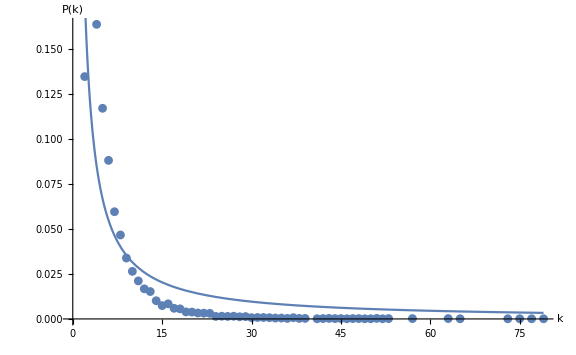

```mathematica
vis2=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"v-2.eps",vis2];
```

## Mean degree

```mathematica
degree=VertexDegree[igv2]//Mean//N;
```

## Record result

```mathematica
(*AppendTo[results, Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];*)
```

## Horizontal Visibility Graph

```mathematica
horizontals={};Do[
Do[
If[horizontalQ[i,j,diffs],AppendTo[horizontals,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
igh2=Graph[horizontals, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igh2];
```

```mathematica
count = Total[adj]//Counts
```

<|1→2,2→3629,3→2482,4→1501,5→879,7→354,6→536,8→234,9→136,14→11,11→59,13→15,12→39,10→105,15→10,16→4,25→1,17→2|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}][[2;;]]
```

{{2,3629/9999},{3,2482/9999},{4,1501/9999},{5,293/3333},{7,118/3333},{6,536/9999},{8,26/1111},{9,136/9999},{14,1/909},{11,59/9999},{13,5/3333},{12,13/3333},{10,35/3333},{15,10/9999},{16,4/9999},{25,1/9999},{17,2/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x];
```

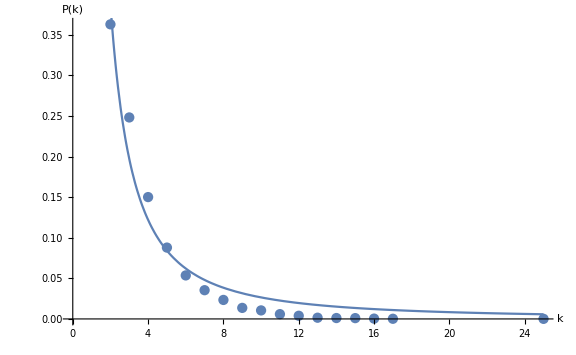

```mathematica
hvis2=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"hv-2.eps",hvis2];
```

## Mean degree

```mathematica
degree=VertexDegree[igh2]//Mean//N;
```

## Record result

```mathematica
(*AppendTo[results, Flatten[{"horizontal", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];*)
```

## Return result

```mathematica
results
```

{}